```mathematica
Get["/usr/tom/Desktop/Summer Research 2016/Necessary Functions.m"]
```

Get::noopen: Cannot open /usr/tom/Desktop/Summer Research 2016/Necessary Functions.m.

$Failed

```mathematica
Module[{wpara,wreg,wsys,plots,img},
wpara=Import["/Users/tomeichlersmith/Desktop/Summer Research 2016/Weird Test Shape/Weird Shape.m"];
wreg=parametricregion[wpara];
wsys=egsystem[6][wreg];
plots=Table[Plot3D[wsys[[2,i]][x,y],{x,y}∈wreg,ViewPoint->{-1,-2,1},Mesh->None,Boxed->False,Axes->False,PlotLabel->wsys[[1,i]]/wsys[[1,1]]],{i,Length[wsys[[2]]]}];
Print[img=GraphicsGrid[{plots[[1;;3]],plots[[4;;6]]},Frame->All,Spacings->0]];
Export["/Users/tomeichlersmith/Desktop/Summer Research 2016/Weird Test Shape/WeirdTest EShapes.jpg",img]]
```

-Graphics-

/Users/tomeichlersmith/Desktop/Summer Research 2016/Weird Test Shape/WeirdTest EShapes.jpg

```mathematica
Module[{sys,plots,img},
sys=egsystem[6][Disk[]];
plots=Table[Plot3D[sys[[2,i]][x,y],{x,y}∈Disk[],ViewPoint->{-1,-2,1},Mesh->None,PlotLabel->sys[[1,i]]/sys[[1,1]],Boxed->False,Axes->False],{i,Length[sys[[2]]]}];
Print[img=GraphicsGrid[{plots[[1;;3]],plots[[4;;6]]},Frame->All,Spacings->0]];
Export["/Users/tomeichlersmith/Desktop/Summer Research 2016/Images/UnitCircle EShapes.jpg",img]]
```

-Graphics-

/Users/tomeichlersmith/Desktop/Summer Research 2016/Images/UnitCircle EShapes.jpg

```mathematica
Module[{sys},
sys=egsystem[6][Disk[]];
frames=Table[
Plot3D[Sin[t]*sys[[2,6]][x,y],{x,y}∈Disk[],ViewPoint->{-1,-2,1},Mesh->None,PlotLabel->sys[[1,6]]/sys[[1,1]],Boxed->False,Axes->False,PlotRange->{-1.7,1.7}],
{t,0,10Pi,0.05}];
Export["/Users/tomeichlersmith/Desktop/Summer Research 2016/EigenFunction Movie.mov",frames]]
```

/Users/tomeichlersmith/Desktop/Summer Research 2016/EigenFunction Movie.mov

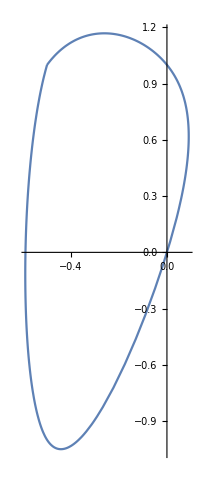

7

```mathematica
Module[{pts,intx,inty},
pts={{0,0},{0,1},{-0.5,1},{-0.5,-1}};
pts=Join[pts,pts[[1;;-1]]];
intx=Interpolation[pts[[All,1]],Method->"Spline"];
inty=Interpolation[pts[[All,2]],Method->"Spline"];
Print[ParametricPlot[{intx[u],inty[u]},{u,3,Length[pts]-1}]];
Print[Length[pts]-1];]
```

```mathematica
tooperf=Import["/Users/tomeichlersmith/Desktop/Summer Research 2016/TooPerfect2beTrue.m"]
```

{10.821,{x1→-0.456514,y1→0.80212,x2→-0.758621,y2→0.704274,x3→-0.624366,y3→0.510365,x4→0.483083,y4→-0.107558,x5→0.641438,y5→-0.146579,x6→0.461706,y6→0.289949}}

```mathematica
Module[{fst,pts},
pts={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6}}/.tooperf[[2]];
fst=FindShortestTour[pts];
tpregion=Polygon[pts[[fst[[2]]]]];
tpsys=egsystem[5][tpregion];
predict[tpsys[[1]]]]
```

2.46916

```mathematica
{fre,tmp}=egsystem[10][Disk[]];
fre/fre[[1]]
```

{1.,1.59337,1.59337,2.13569,2.13572,2.29569,2.65353,2.65354,2.91819,2.91821}

```mathematica
meas={341.,554,786,867,1015};
meas/meas[[1]]
```

{1.,1.62463,2.30499,2.54252,2.97654}

```mathematica
mea={892.,924.,1168.,1669,2219.};
mea/mea[[1]]
```

{1.,1.03587,1.30942,1.87108,2.48767}